## 几何

## 距离

欧几里得距离

```mathematica
EuclideanDistance[{a,b,c},{x,y,z}]
```

√(Abs[a-x]^2+Abs[b-y]^2+Abs[c-z]^2)

```mathematica
EuclideanDistance[{1,2,3},{2,4,6}]
```

√14

欧氏距离平方

```mathematica
SquaredEuclideanDistance[{a,b,c},{x,y,z}]
```

Abs[a-x]^2+Abs[b-y]^2+Abs[c-z]^2

```mathematica
SquaredEuclideanDistance[{1,2,3},{2,4,6}]
```

14

曼哈顿距离

```mathematica
ManhattanDistance[{a,b,c},{x,y,z}]
```

Abs[a-x]+Abs[b-y]+Abs[c-z]

```mathematica
ManhattanDistance[{1,2,3},{2,4,6}]
```

6

切比雪夫距离

```mathematica
ChessboardDistance[{a,b,c},{x,y,z}]
```

Max[Abs[a-x],Abs[b-y],Abs[c-z]]

```mathematica
ChessboardDistance[{1,2,3},{2,4,6}]
```

3

闵可夫斯基距离

```mathematica
MinkowskiDistance[a_List,b_List,p_]:=Norm[a-b,p]
```

将闵氏距离化归为其他距离

```mathematica
MinkowskiDistance[{a,b,c},{x,y,z},#]&/@{1,2,Infinity}
```

{Abs[a-x]+Abs[b-y]+Abs[c-z],√(Abs[a-x]^2+Abs[b-y]^2+Abs[c-z]^2),Max[Abs[a-x],Abs[b-y],Abs[c-z]]}

可视化

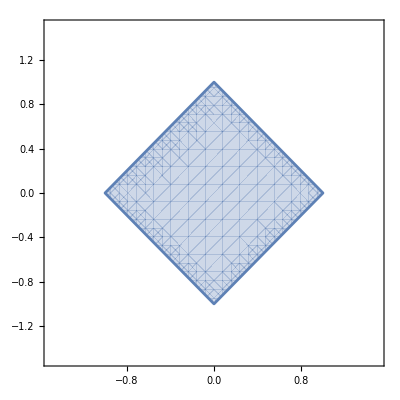
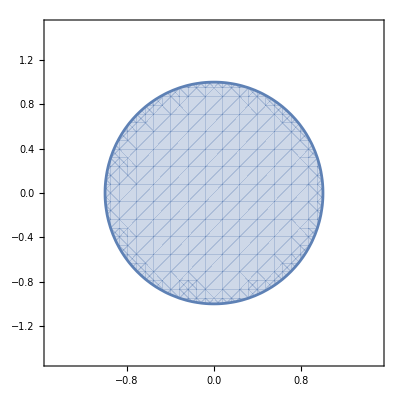
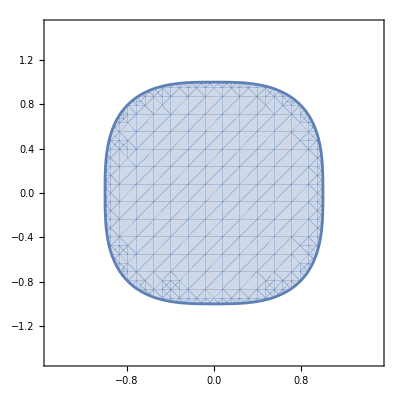
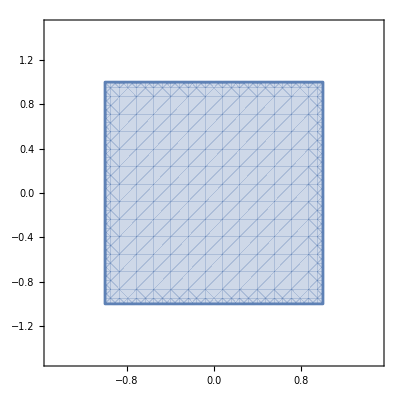

```mathematica
Table[RegionPlot[Norm[{x,y},p]<=1,{x,-1.5,1.5},{y,-1.5,1.5},FrameTicks->None],{p,{1,2,3,Infinity}}]
```

```mathematica
Table[Plot3D[Norm[{x,y},p],{x,-1.5,1.5},{y,-1.5,1.5},Mesh->None,Ticks->None],{p,{1,2,3,Infinity}}]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

## 平面几何变换

非线性变换

```mathematica
ℛ=TransformedRegion[Disk[{1,1},4],{Indexed[#,1] Indexed[#,2],Indexed[#,1]+Indexed[#,2]}&];
```

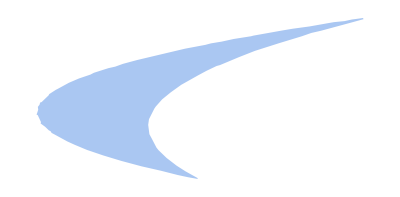
{-Graphics-,(128 √2)/3}

```mathematica
#[ℛ]&/@{Region,RegionMeasure}
```

投影

```mathematica
v={-1,3};l={1,1};
p=Projection[v,l]
```

{1,1}

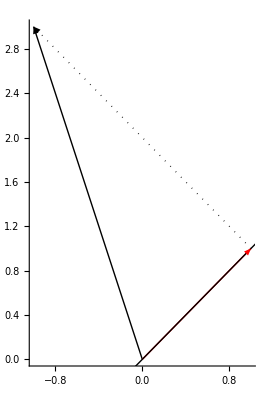

```mathematica
Graphics[{InfiniteLine[{0,0},l],Arrow[{{0,0},v}],Directive[Red,Thick],Arrow[{{0,0},p}],Directive[Black,Dotted],Arrow[{p,v}]},PlotRangePadding->.5,Axes->True]
```

## 立体几何变换

欧拉角

```mathematica
{x1,y1,z1}={{1,0,0},{0,1,0},{0,0,1}};
{x2,y2,z2}=RotationTransform[π/3,{1,0,0}][{x1,y1,z1}];
```

```mathematica
R={x2,y2,z2}ᵀ.{x1,y1,z1};
```

```mathematica
{x2,y2,z2}ᵀ==R.{x1,y1,z1}ᵀ//Simplify
```

True

```mathematica
EulerAngles[R]
```

{-π/2,π/3,π/2}

```mathematica
billboard[s_,p_]:=Inset[Framed[s,Background->LightGray],p];
```

```mathematica
s1={{Arrow[{{0,0,0},x1}],billboard["X",x1]},{Arrow[{{0,0,0},y1}],billboard["Y",y1]},{Arrow[{{0,0,0},z1}],billboard["Z",z1]}};
```

```mathematica
s2={{Red,Arrow[{{0,0,0},x2}],billboard["X",x2]},{Green,Arrow[{{0,0,0},y2}],billboard["Y",y2]},{Blue,Arrow[{{0,0,0},z2}],billboard["Z",z2]}};
```

```mathematica
Show[Graphics3D[#,ViewPoint->{2,1,1}]&/@{s1,s2}]
```

-Graphics3D-

立体图形的投影

```mathematica
ResourceFunction["ProjectGraphics3D"][ Graphics3D@ResourceFunction["PrimitiveToPolygons"][Dodecahedron[]], {1,1,-1}]
```

-Graphics3D-

## 奇异值分解

Case 1

```mathematica
{u,s,v}=SingularValueDecomposition[{{5/4,-3/4},{-3/4,5/4}}];
```

```mathematica
points0=Table[{i,j},{i,-5,5},{j,-5,5}]//Flatten[#,1]&;
```

```mathematica
points1=ConjugateTranspose[v].#&/@points0;
```

```mathematica
points2=s.#&/@points1;
```

```mathematica
points3=u.#&/@points2;
```

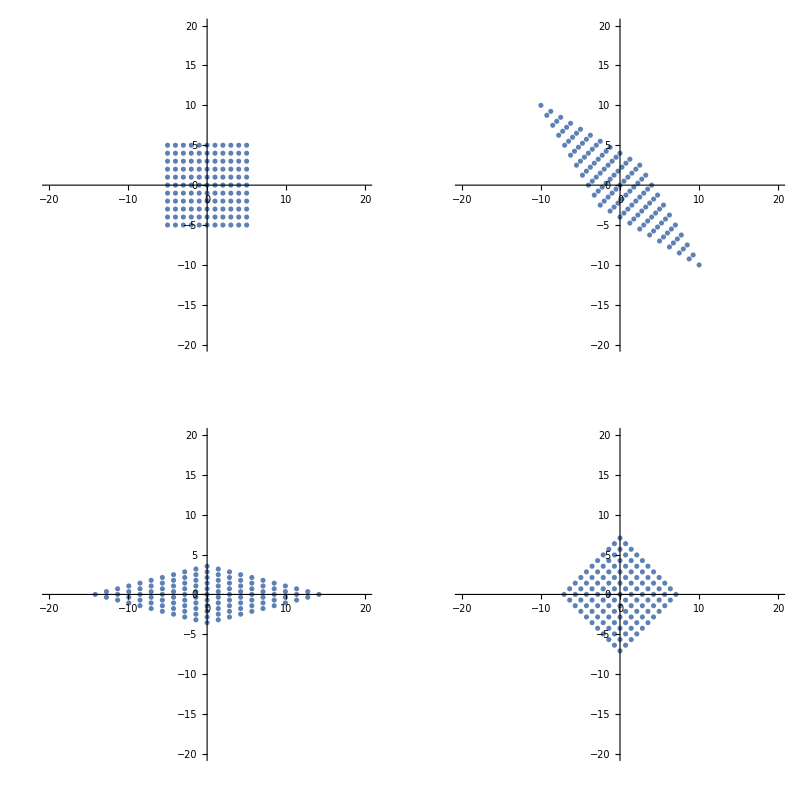

```mathematica
ListPlot[#,PlotRange->{{-20,20},{-20,20}},AspectRatio->1]&/@{points0,points3,points2,points1}//ArrayReshape[#,{2,2}]&//GraphicsGrid
```

Case 2

```mathematica
{u,s,v}=SingularValueDecomposition[{{0,1,-1},{1,0,-1},{1,1,0}}];
```

```mathematica
points0=Table[{i,j,k},{i,-5,5},{j,-5,5},{k,-5,5}]//Flatten[#,2]&;
```

```mathematica
points1=ConjugateTranspose[v].#&/@points0;
```

```mathematica
points2=s.#&/@points1;
```

```mathematica
points3=u.#&/@points2;
```

```mathematica
ListPointPlot3D[#,PlotRange->{{-10,10},{-10,10},{-10,10}},AspectRatio->1]&/@{points0,points3,points2,points1}//ArrayReshape[#,{2,2}]&//GraphicsGrid
```

-Graphics-

Case 3

```mathematica
{u,s,v}=SingularValueDecomposition[{{0,1},{1,0},{-1,-1}}];
```

```mathematica
points0=Table[{i,j},{i,-5,5},{j,-5,5}]//Flatten[#,1]&;
```

```mathematica
points1=ConjugateTranspose[v].#&/@points0;
```

```mathematica
points2=s.#&/@points1;
```

```mathematica
points3=u.#&/@points2;
```

```mathematica
GraphicsGrid[{{ListPlot[points0,AspectRatio->1],ListPointPlot3D[points3,AspectRatio->1]},{ListPlot[points1,AspectRatio->1],ListPointPlot3D[points2,AspectRatio->1]}}]
```

-Graphics-

Case 4

```mathematica
{u,s,v}=SingularValueDecomposition[{{0,1,1},{1,1,0}}];
```

```mathematica
points0=Table[{i,j,k},{i,-5,5},{j,-5,5},{k,-5,5}]//Flatten[#,2]&;
```

```mathematica
points1=ConjugateTranspose[v].#&/@points0;
```

```mathematica
points2=s.#&/@points1;
```

```mathematica
points3=u.#&/@points2;
```

```mathematica
GraphicsGrid[{{ListPointPlot3D[points0,AspectRatio->1],ListPlot[points3,AspectRatio->1]},{ListPointPlot3D[points1,AspectRatio->1],ListPlot[points2,AspectRatio->1]}}]
```

-Graphics-

总结一个函数

```mathematica
SVDVisualization[matrix_]:=Module[{u,s,v,points0,points1,points2,points3,n,plotPoints,plots},(*Perform SVD on the matrix*){u,s,v}=SingularValueDecomposition[matrix];
(*Determine the number of columns of the matrix*)
n=Dimensions[matrix][[2]];
(*Generate points0 in n-dimensional space*)
points0=If[n==2,Table[{i,j},{i,-5,5},{j,-5,5}]//Flatten[#,1]&,Table[{i,j,k},{i,-5,5},{j,-5,5},{k,-5,5}]//Flatten[#,2]&];
(*Transform points through SVD steps*)
points1=ConjugateTranspose[v].#&/@points0;
points2=s.#&/@points1;
points3=u.#&/@points2;
(*Define the plotting function based on point dimension*)plotPoints[pts_]:=If[Length[First[pts]]==2,ListPlot[pts,PlotRange->{{-20,20},{-20,20}},AspectRatio->1],ListPointPlot3D[pts,PlotRange->{{-10,10},{-10,10},{-10,10}},AspectRatio->1]];
(*Generate plots for each set of points*)
plots={plotPoints[points0],plotPoints[points3],plotPoints[points2],plotPoints[points1]};
(*Arrange plots in a 2x2 grid*)
GraphicsGrid[Partition[plots,2]]]
```

## 瑞利商

### 二元瑞利商

写一个可视化函数

```mathematica
RayleighQuotientPlot[a_,b_,c_]:=Block[{qmatrix,func,x,y,eigVecs,unitCircle,arrows},qmatrix={{a,b},{b,c}};
func=(a x^2+2 b x y+c y^2)/(x^2+y^2);
(*计算特征向量*)
eigVecs=Eigenvectors[qmatrix];
(*单位圆*)
unitCircle=ParametricPlot[{Cos[t],Sin[t]},{t,0,2 Pi},PlotStyle->{Thick,Black}];
(*特征向量箭头*)
arrows=Graphics[{Black,Thick,Arrow[{{0,0},Normalize[eigVecs[[1]]]}],Black,Thick,Arrow[{{0,0},Normalize[eigVecs[[2]]]}]}];
(*组合图形*)
{Show[DensityPlot[func,{x,-2,2},{y,-2,2},PlotPoints->50,ColorFunction->"TemperatureMap",PlotRange->All],unitCircle,arrows,PlotRange->{{-2,2},{-2,2}}],Plot3D[func,{x,-2,2},{y,-2,2},ColorFunction->"TemperatureMap"]}]
```

```mathematica
RayleighQuotientPlot@@@{{1,0,2},{3/2,1/2,3/2},{-1,0,-2},{-3/2,-1/2,-3/2}}
```

```mathematica
RayleighQuotientPlot@@@{{1,-1,1},{-1,1,-1},{1,0,-1},{0,2,0}}
```

在单位圆上看二元瑞利商，Filling 的语法很关键

```mathematica
RayleighQuotientThetaPlot[a_,b_,c_]:=Block[{qmatrix,func,x,y,theta,maxVal,minVal},qmatrix={{a,b},{b,c}};
func=(a x^2+2 b x y+c y^2)/(x^2+y^2)/. {x->Cos@theta,y->Sin@theta};
maxVal=NMaxValue[{func,0<=theta<=2 Pi},theta];minVal=NMinValue[{func,0<=theta<=2 Pi},theta];
Plot[func,{theta,0,2 Pi},PlotRange->{-2,2},Filling->{1->minVal,1->maxVal},PlotTheme->"Detailed",PlotLegends->None]]
```

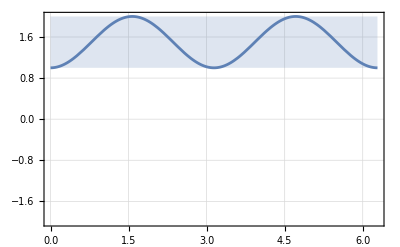
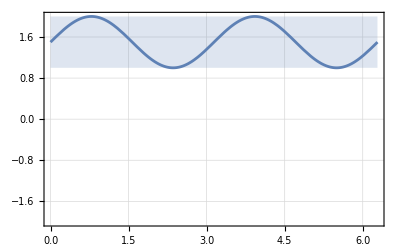
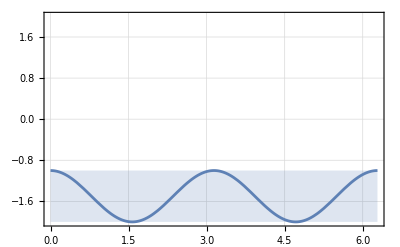
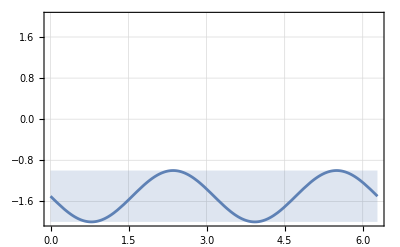

```mathematica
RayleighQuotientThetaPlot@@@{{1,0,2},{3/2,1/2,3/2},{-1,0,-2},{-3/2,-1/2,-3/2}}
```

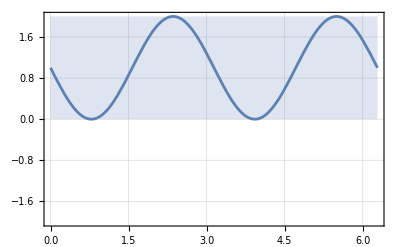
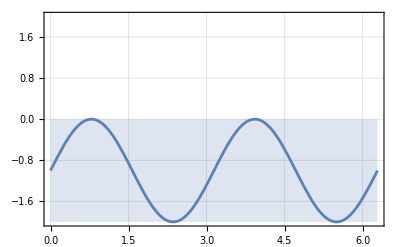
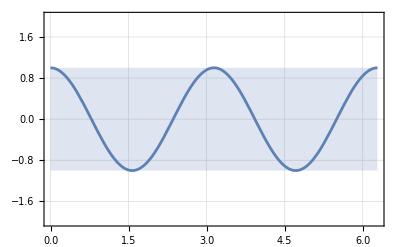
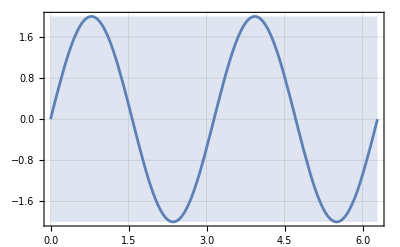

```mathematica
RayleighQuotientThetaPlot@@@{{1,-1,1},{-1,1,-1},{1,0,-1},{0,2,0}}
```

### 三元瑞利商

在单位球上绘制三元瑞利商，并使用球坐标系绘制 θ-φ 平面

```mathematica
RayleighQuotientDensityPlot3D[A_?MatrixQ]:={SliceDensityPlot3D[{x,y,z}.A.{x,y,z},x^2+y^2+z^2==1,{x,-1,1},{y,-1,1},{z,-1,1},PlotPoints->50,ColorFunction->"TemperatureMap",PlotLegends->Automatic,Axes->False,Boxed->False],Module[{R,θ,φ},R[θ_,φ_]:={Sin[θ] Cos[φ],Sin[θ] Sin[φ],Cos[θ]}.A.{Sin[θ] Cos[φ],Sin[θ] Sin[φ],Cos[θ]};
DensityPlot[R[θ,φ],{φ,0,2π},{θ,0,π},ColorFunction->"TemperatureMap",PlotLegends->None,FrameLabel->{"φ","θ"},PlotPoints->50,AspectRatio->1/2]]}//GraphicsRow
```

```mathematica
RayleighQuotientDensityPlot3D/@DiagonalMatrix/@{{1,2,3},{1,0,3},-{1,2,3},-{1,0,3}}
```

```mathematica
RayleighQuotientDensityPlot3D/@Prepend[DiagonalMatrix/@{{1,-2,3},{1,1,-1},{1,0,-1}},{{0,1,0},{1,0,0},{0,0,0}}]
```

球面上的等高线图

```mathematica
RayleighQuotientContourPlot3D[A_?MatrixQ]:={SliceContourPlot3D[{x,y,z}.A.{x,y,z},x^2+y^2+z^2==1,{x,-1,1},{y,-1,1},{z,-1,1},PlotPoints->50,ColorFunction->"TemperatureMap",PlotLegends->Automatic,Axes->False,Boxed->False,ContourStyle->White],Module[{R,θ,φ},R[θ_,φ_]:={Sin[θ] Cos[φ],Sin[θ] Sin[φ],Cos[θ]}.A.{Sin[θ] Cos[φ],Sin[θ] Sin[φ],Cos[θ]};
ContourPlot[R[θ,φ],{φ,0,2π},{θ,0,π},ColorFunction->"TemperatureMap",PlotLegends->None,FrameLabel->{"φ","θ"},PlotPoints->50,AspectRatio->1/2,ContourStyle->White]]}//GraphicsRow
```

```mathematica
RayleighQuotientContourPlot3D/@DiagonalMatrix/@{{1,2,3},{1,0,3},-{1,2,3},-{1,0,3}}
```

```mathematica
RayleighQuotientContourPlot3D/@Prepend[DiagonalMatrix/@{{1,-2,3},{1,1,-1},{1,0,-1}},{{0,1,0},{1,0,0},{0,0,0}}]
```

类似于世界地图的圆柱投影

```mathematica
GeoProjectionData["Cylindrical"]
```

{ArdenClose,Balthasart,BehrmannEqualArea,BraunCylindrical,BraunII,BSAMCylindrical,Cassini,CrasterCylindricalEqualArea,CylindricalEqualArea,CylindricalEquidistant,CylindricalPerspective,CylindricalSatelliteTracking,Equirectangular,GallIsographic,GallStereographic,HoboDyer,KarchenkoShabanova,LambertCylindrical,Mercator,MillerCylindrical,MillerCylindricalII,MillerPerspective,ObliqueMercator,ObliqueMercatorNGS,PavlovCylindrical,ToblerI,ToblerII,TransverseMercator,TrystanEdwards,UrmayevCylindricalII,UrmayevCylindricalIII}

```mathematica
GeoGraphics[GeoRange->"World",GeoProjection->"Equirectangular"]
```

-Graphics-

## 心形线

循环图

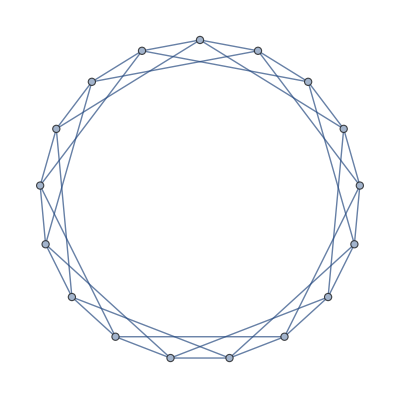
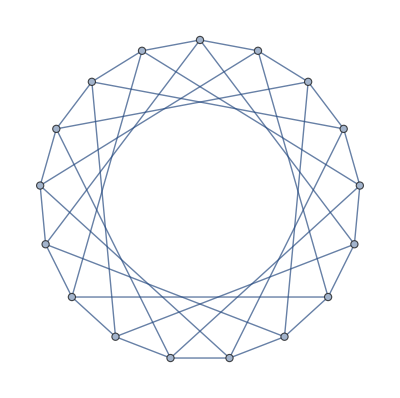
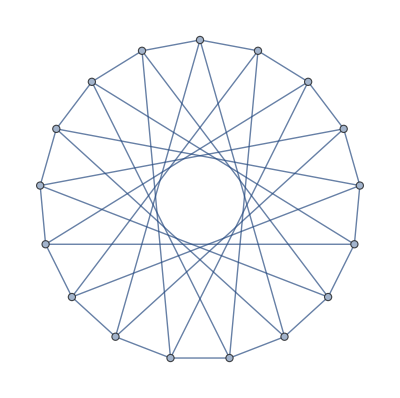
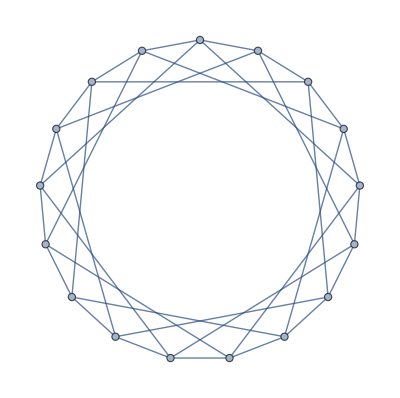

```mathematica
Table[CirculantGraph[17,{1,k}],{k,{3,5,10,13}}]
```

心形线

黑色线条

```mathematica
drawCardioid[numPoints_Integer,multiplier_Integer,"Black"]:=Module[{points,connections},points=Table[{Cos[2 Pi n/numPoints],Sin[2 Pi n/numPoints]},{n,0,numPoints-1}];
connections=Table[Line[{points[[n+1]],points[[Mod[multiplier (n+1),numPoints]+1]]}],{n,0,numPoints-1}];
Graphics[{PointSize[Small],Point[points],connections}]]
```

HSV彩色渲染

```mathematica
drawCardioid[numPoints_Integer,multiplier_Integer]:=Module[{points,connections},points=Table[{Cos[2 Pi n/numPoints],Sin[2 Pi n/numPoints]},{n,0,numPoints-1}];
connections=Table[With[{color=Hue[n/numPoints]},{color,Line[{points[[n+1]],points[[Mod[multiplier (n+1),numPoints]+1]]}]}],{n,0,numPoints-1}];
Graphics[{PointSize[Small],Point[points],connections}]]
```

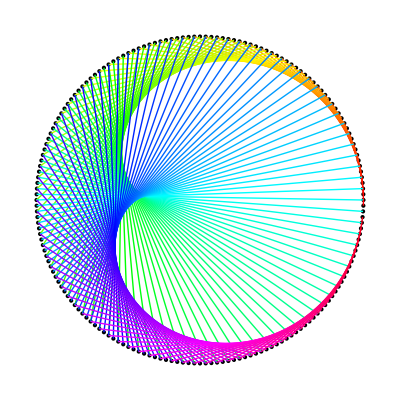
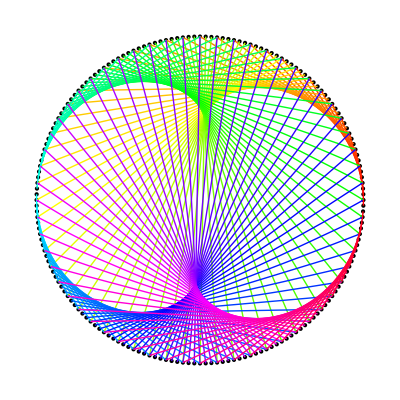
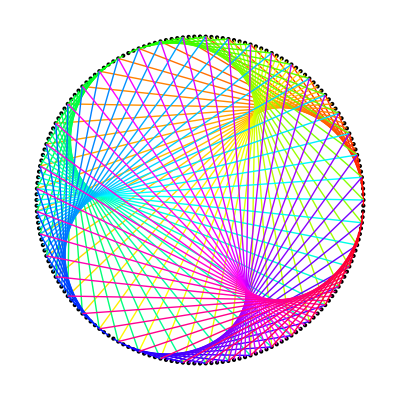
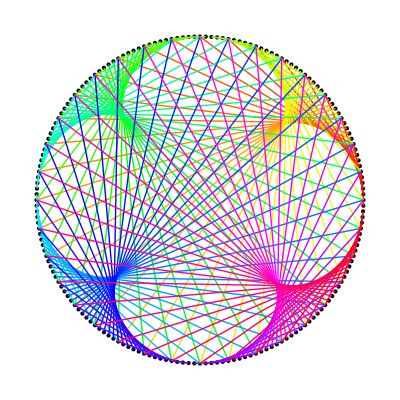
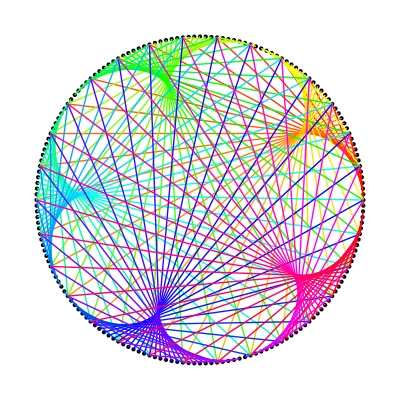
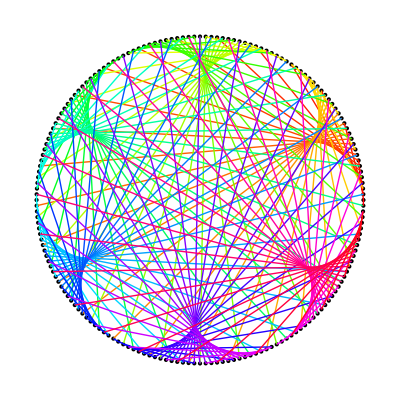

```mathematica
drawCardioid[180,#]&/@Range[2,7]
```

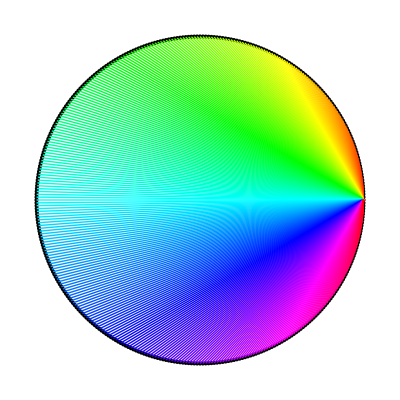
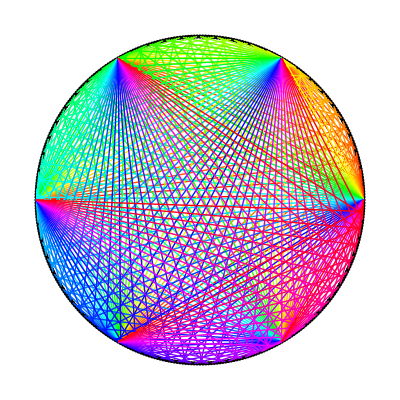
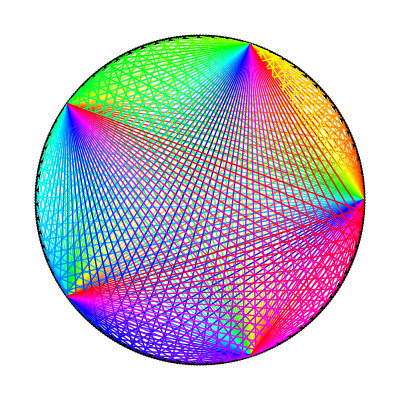
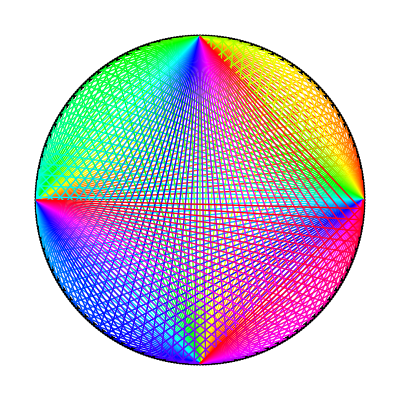
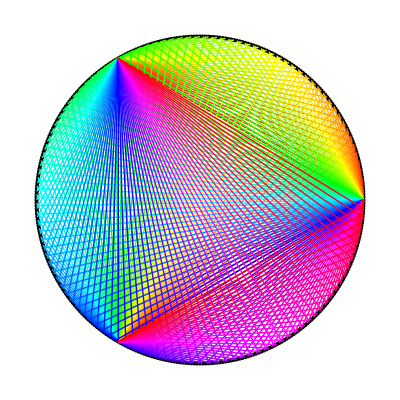
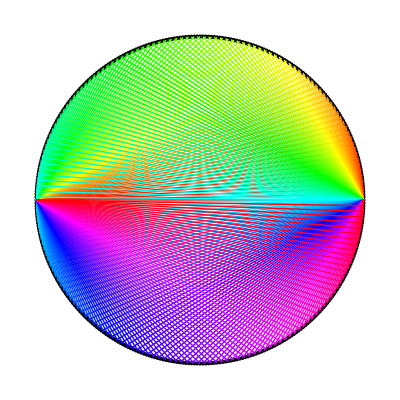

```mathematica
drawCardioid[360,#]&/@{0,60,72,90,120,180}
```

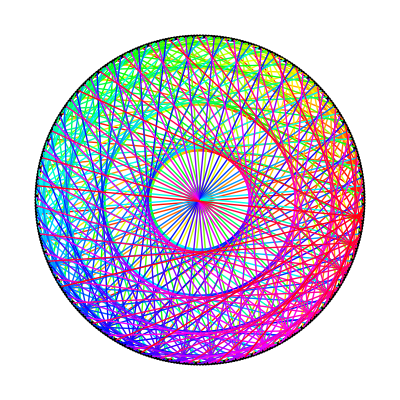
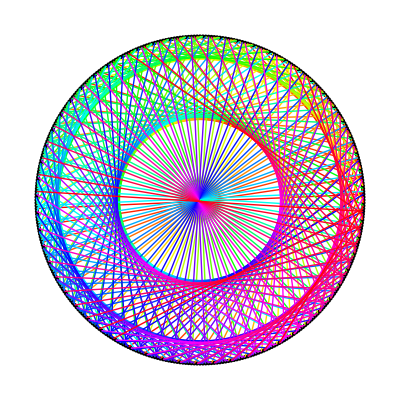
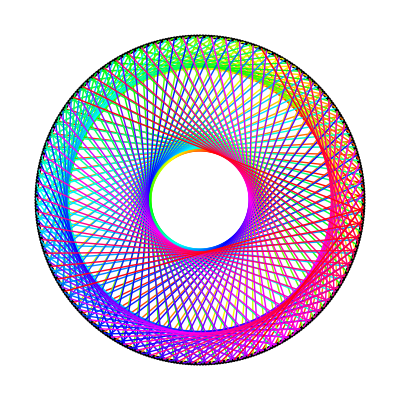
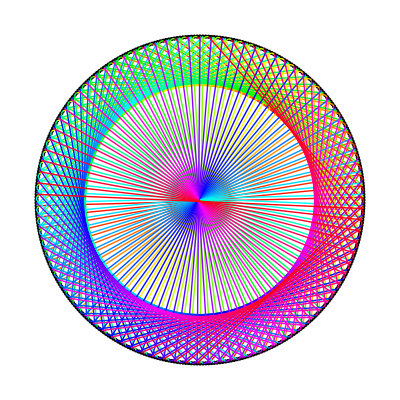
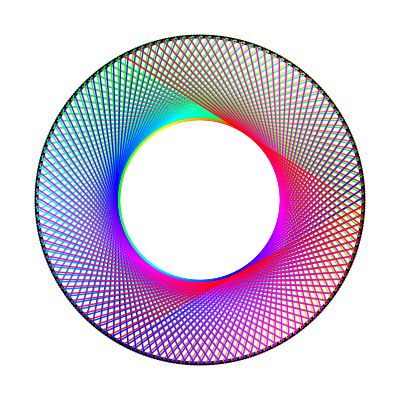
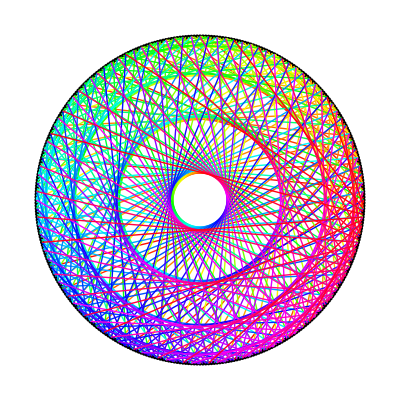

```mathematica
drawCardioid[360,#]&/@{37,61,73,91,121,321}
```

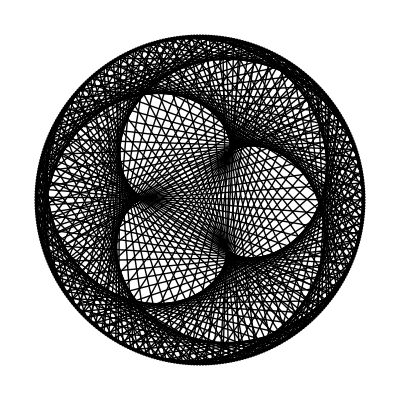
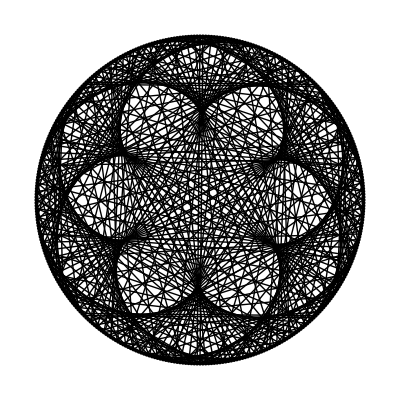
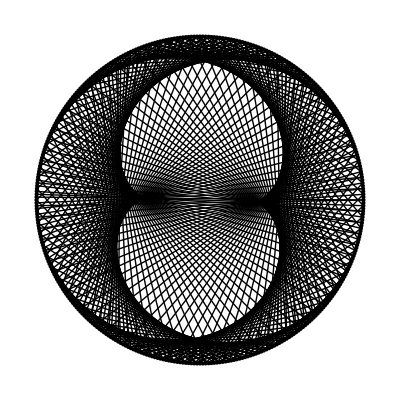
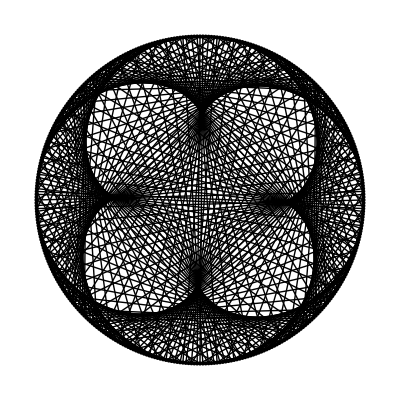
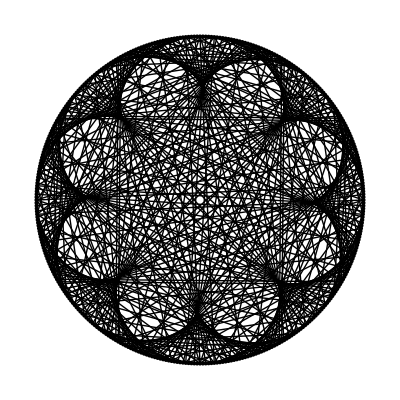
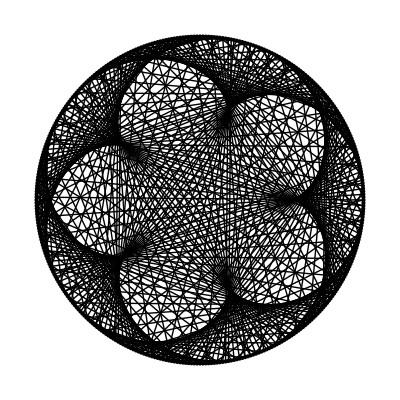

```mathematica
drawCardioid[360,#,"Black"]&/@{122,123,182,183,185,206}
```

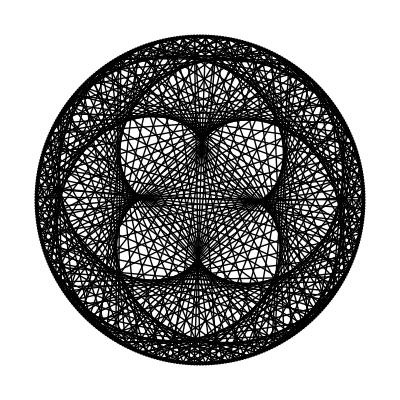
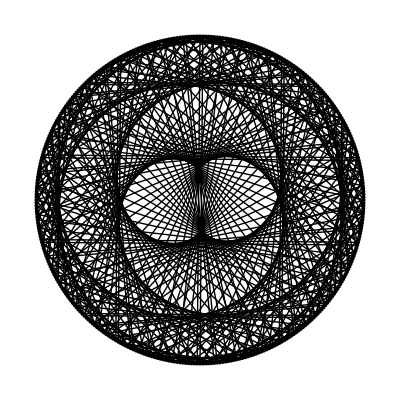
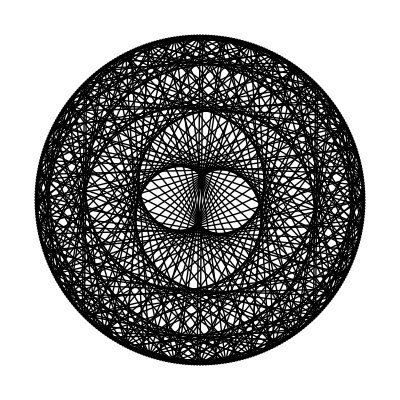
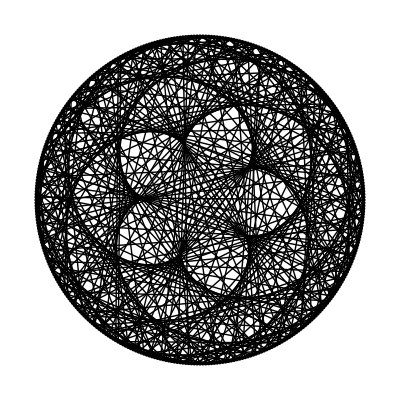
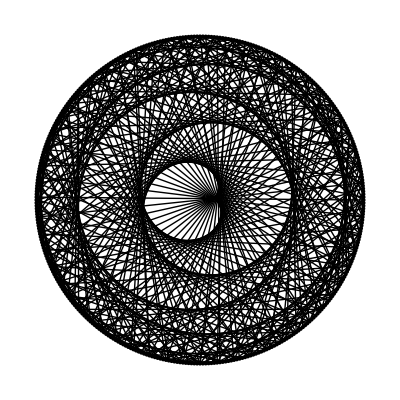
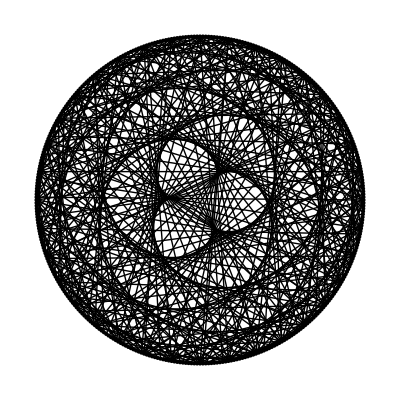

```mathematica
drawCardioid[360,#,"Black"]&/@{92,155,207,218,258,310}
```